## Distribution of D_discrete(t_1,t_2) over D_field(t_1,t_2) as a density

```mathematica
filepathfield="/run/user/1000/gvfs/sftp:host=spine.tphys.uni-linz.ac.at,user=miethlinger/itpraid/miethlinger/University/Master/MasterThesis/Programming/FieldRecurrences/Resources/results/60000_1_200_10000/elements/recurrencematrix.txt";
filepathhungarian="/run/user/1000/gvfs/sftp:host=spine.tphys.uni-linz.ac.at,user=miethlinger/itpraid/miethlinger/University/Master/MasterThesis/Programming/Hungarian Method/Resources/results/60000_100_5000_1_200_10000/elements/recurrencematrix.txt";
```

```mathematica
costmatrixfield=Map[Internal`StringToDouble[#]&,Map[StringSplit@#&,Import[filepathfield,"List"]],{2}];
costmatrixhungarian=Map[Internal`StringToDouble[#]&,Map[StringSplit@#&,Import[filepathhungarian,"List"]],{2}];
costmatrixcomb=Flatten[{costmatrixfield,costmatrixhungarian},{{2},{3},{1}}];
costmatrixpairs=Sort[Flatten[costmatrixcomb,1],#1[[1]]>#2[[1]]&];
```

```mathematica
G[r_,δr_]:=HeavisideLambda[r/δr];
δ=25;
min=0+δ/2;
max=8*10^3-δ/2;
indexlist=Map[(Round[#-δ/2,δ]+δ/2)&,costmatrixpairs];
n=(max-min)/δ+1;
Clear@ρ;
Evaluate@Table[ρ[x,y],{x,min,max,δ},{y,min,max,δ}]=Table[0,{x,min,max,δ},{y,min,max,δ}];
length=Length@indexlist;
```

```mathematica
Do[
ρ[indexlist[[i,1]],indexlist[[i,2]]]+=1;
,{i,length}];

dataxy=Table[ρ[x,y],{x,min,max,δ},{y,min,max,δ}];
kernel=Table[G[Norm[{x,y}],5*δ],{x,-5*δ,5*δ,δ},{y,-5*δ,5*δ,δ}];
dataxyconv=ListConvolve[kernel,dataxy];
dataxyconvscaled=N[dataxyconv/Max@dataxyconv];
xyfield=Table[{x,y},{x,min,max,δ},{y,min,max,δ}];
dataxyconvscaledfull=Flatten[MapIndexed[{xyfield[[#2[[1]],#2[[2]]]][[1]],xyfield[[#2[[1]],#2[[2]]]][[2]],#1}&,dataxyconvscaled,{2}],1];
```

```mathematica
label[1][0]=DisplayForm@Row[{
SubscriptBox[Style["D",FontFamily->"CMU Serif",Italic,40],Style["field",FontFamily->"CMU Serif",Plain,20]],Row[{Style["(",FontFamily->"CMU Serif",Italic,40],SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,40],Style["1",FontFamily->"CMU Serif",Plain,20]],
Style[",",FontFamily->"CMU Serif",Plain,40],SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,40],Style["2",FontFamily->"CMU Serif",Plain,20]],Style[")",FontFamily->"CMU Serif",Italic,40]}]}]

label[1][1]=DisplayForm@Row[{
SubscriptBox[Style["D",FontFamily->"CMU Serif",Italic,40],Style["discrete",FontFamily->"CMU Serif",Plain,20]],Row[{Style["(",FontFamily->"CMU Serif",Italic,40],SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,40],Style["1",FontFamily->"CMU Serif",Plain,20]],
Style[",",FontFamily->"CMU Serif",Plain,40],SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,40],Style["2",FontFamily->"CMU Serif",Plain,20]],Style[")",FontFamily->"CMU Serif",Italic,40]}]}]
```

D_field(t_1,t_2)

D_discrete(t_1,t_2)

```mathematica
filepathoutd1d2="/run/user/1000/gvfs/sftp:host=spine.tphys.uni-linz.ac.at,user=miethlinger/itpraid/miethlinger/University/Master/MasterThesis/Programming/Comparator/images/d1d2_compare/";
g1[1]=ArrayPlot[
1.2*dataxyconvscaledᵀ,
PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],
FrameLabel->{label[1][1],label[1][0]},
FrameTicks->{{Table[{x/δ,x},{x,0,max,40*δ}],None},{Table[{x/δ,x},{x,0,max,40*δ}],None}},
DataReversed->{True,False},
ImageSize->{1000,1000},ColorFunctionScaling->False,ColorFunction->GrayLevel,PlotLegends->BarLegend[{Automatic,{0,1}},LegendLayout->"Column",LegendMarkerSize->{25,946},LabelStyle->Directive[Black,FontColor->Black,30,FontFamily->"CMU Serif"],LegendMargins->{{14,0},{67,0}}]
];
Export[filepathoutd1d2<>"d1d2_gray.png",g1[1],"PNG",ImageResolution->400];
MyColor[z_]:=ColorData["TemperatureMap"][z];
g1[2]=ArrayPlot[
1.2*dataxyconvscaledᵀ,
PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],
FrameLabel->{label[1][1],label[1][0]},
FrameTicks->{{Table[{x/δ,x},{x,0,max,40*δ}],None},{Table[{x/δ,x},{x,0,max,40*δ}],None}},
DataReversed->{True,False},
ImageSize->{1000,1000},ColorFunctionScaling->False,ColorFunction->MyColor,PlotLegends->BarLegend[{Function[z,MyColor[z]],{0,1}},LegendLayout->"Column",LegendMarkerSize->{25,946},LabelStyle->Directive[Black,FontColor->Black,30,FontFamily->"CMU Serif"],LegendMargins->{{14,0},{67,0}}]
];
Export[filepathoutd1d2<>"d1d2_mycolor.png",g1[2],"PNG",ImageResolution->400];
g1[3]=ArrayPlot[
1.2*dataxyconvscaledᵀ,
PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],
FrameLabel->{label[1][1],label[1][0]},
FrameTicks->{{Table[{x/δ,x},{x,0,max,40*δ}],None},{Table[{x/δ,x},{x,0,max,40*δ}],None}},
DataReversed->{True,False},
ImageSize->{1000,1000},ColorFunctionScaling->False,PlotLegends->BarLegend[{Automatic,{0,1}},LegendLayout->"Column",LegendMarkerSize->{25,946},LabelStyle->Directive[Black,FontColor->Black,30,FontFamily->"CMU Serif"],LegendMargins->{{14,0},{67,0}}]
];
Export[filepathoutd1d2<>"d1d2_scientific.png",g1[3],"PNG",ImageResolution->400];
```

```mathematica
(* Dump for this section *)
(* diffmatrix=Map[#[[1]]-#[[2]]&,costmatrixcomb,{2}]; *)
(* f[x_]=Fit[costmatrixpairs,{1,x},x]; *)
(* ListPlot[costmatrixpairs,PlotRange->{{0,10000},{0,10000}}] *)
(* Too slow *)
(* ρD1D2[{x_,y_},δr_]=Total[Map[G[Norm[{x,y}-#],δr]&,costmatrixpairs]]; *)
(* filepathfield=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"FieldRecurrences","Resources","results","60000_1_200_10000","elements","recurrencematrix.txt"}] *)
(* filepathhungarian=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Hungarian Method","Resources","results","60000_100_5000_1_200_10000","elements","recurrencematrix.txt"}] *)
```

### Distribution of D_discrete(t_1,t_2)/D_field(t_1,t_2) over D_field(t_1,t_2) as a PDF / CDF

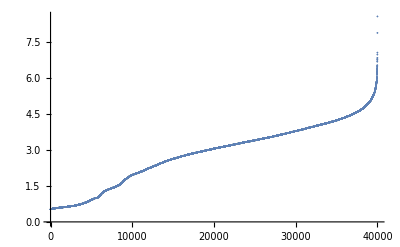

```mathematica
costmatrixfactors=Sort[Map[If[#[[2]]==0||#[[1]]==0,1,#[[1]]/#[[2]]]&,costmatrixpairs],#1<#2&];
ListPlot[costmatrixfactors,PlotRange->All]
```

## Comparison of D_field(t_1;t_2) and D_discrete(t_1;t_2) per rows

```mathematica
filepathoutrowcompare="/run/user/1000/gvfs/sftp:host=spine.tphys.uni-linz.ac.at,user=miethlinger/itpraid/miethlinger/University/Master/MasterThesis/Programming/Comparator/images/row_compare/";
```

```mathematica
label[2][1]=DisplayForm@Row[{
Style["D",FontFamily->"CMU Serif",Italic,40],Row[{Style["(",FontFamily->"CMU Serif",Italic,40],SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,40],Style["1",FontFamily->"CMU Serif",Plain,20]],
Style[";",FontFamily->"CMU Serif",Plain,30],SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,40],Style["2",FontFamily->"CMU Serif",Plain,20]],Style[")",FontFamily->"CMU Serif",Italic,40]}]}]

label[2][2]=DisplayForm@Row[{
SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,40],Style["1",FontFamily->"CMU Serif",Plain,20]],
Style[" [s]",FontFamily->"CMU Serif",40]
}]

label[2][3]=DisplayForm@Row[{
SubscriptBox[Style["D",FontFamily->"CMU Serif",Italic,36],Style["field",FontFamily->"CMU Serif",Plain,16]],
Row[{
Style["(",FontFamily->"CMU Serif",Italic,36],
SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,36],Style["1",FontFamily->"CMU Serif",Plain,20]],
Style[";",FontFamily->"CMU Serif",Plain,27],
SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,36],Style["2",FontFamily->"CMU Serif",Plain,20]],
Style[")",FontFamily->"CMU Serif",Italic,36]
}],
Style[" [1]",FontFamily->"CMU Serif",40,Plain]
}]

label[2][4]=DisplayForm@Row[{
Style["c·",FontFamily->"CMU Serif",Italic,36],
SubscriptBox[Style["D",FontFamily->"CMU Serif",Italic,36],Style["discrete",FontFamily->"CMU Serif",Plain,16]],
Row[{
Style["(",FontFamily->"CMU Serif",Italic,36],
SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,36],Style["1",FontFamily->"CMU Serif",Plain,20]],
Style[";",FontFamily->"CMU Serif",Plain,27],
SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,36],Style["2",FontFamily->"CMU Serif",Plain,20]],Style[")",FontFamily->"CMU Serif",Italic,36]
}],
Style[" [m]",FontFamily->"CMU Serif",40,Plain]
}]

label[2][5]=DisplayForm@Row[{
SubscriptBox[Style["Δ",FontFamily->"CMU Serif",Plain,36],Style["D",FontFamily->"CMU Serif",Italic,20]],Row[{Style["(",FontFamily->"CMU Serif",Italic,36],SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,36],Style["1",FontFamily->"CMU Serif",Plain,20]],
Style[";",FontFamily->"CMU Serif",Plain,27],SubscriptBox[Style["t",FontFamily->"CMU Serif",Italic,36],Style["2",FontFamily->"CMU Serif",Plain,20]],Style[")",FontFamily->"CMU Serif",Italic,36]}]}]
```

D(t_1;t_2)

t_1 [s]

D_field(t_1;t_2) [1]

c·D_discrete(t_1;t_2) [m]

Δ_D(t_1;t_2)

```mathematica
filepathoutrowcompare="/run/user/1000/gvfs/sftp:host=spine.tphys.uni-linz.ac.at,user=miethlinger/itpraid/miethlinger/University/Master/MasterThesis/Programming/Comparator/images/row_compare/";
Do[
s=t/.NMaximize[Total[Map[If[LessEqual[#,500],1,0]&,Abs[costmatrixfield[[i]]-t*costmatrixhungarian[[i]]]]],t][[2]];

g2=ListLinePlot[{costmatrixfield[[i]],s*costmatrixhungarian[[i]],Abs[costmatrixfield[[i]]-s*costmatrixhungarian[[i]]]},PlotRange->All,
PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],
FrameTicks->{{Automatic,None},{Table[{t+KroneckerDelta[t,0],t/40.},{t,0,200,50}],None}},
ImageSize->{1000,1000}*{1,GoldenRatio^-1},
ImagePadding->{{140,25},{90,0}},
ColorFunctionScaling->False,
FrameLabel->{label[2][2],label[2][1]},
PlotLegends->Placed[{label[2][3],label[2][4],label[2][5]},{0.795,0.81}]
];
Export[filepathoutrowcompare<>"row_compare_"<>ToString[i*10^4]<>".png",g2,"PNG",ImageResolution->300]

,{i,10,Length@costmatrixfield,10}] ;
```

```mathematica
i=20;
s=t/.NMaximize[Total[Map[If[LessEqual[#,500],1,0]&,Abs[costmatrixfield[[i]]-t*costmatrixhungarian[[i]]]]],t][[2]];
g2=ListLinePlot[{costmatrixfield[[i]],s*costmatrixhungarian[[i]],Abs[costmatrixfield[[i]]-s*costmatrixhungarian[[i]]]},PlotRange->All,
PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],
FrameTicks->{{Automatic,None},{Table[{t+KroneckerDelta[t,0],t/40.},{t,0,200,50}],None}},
ImageSize->{1000,1000}*{1,GoldenRatio^-1},
ImagePadding->{{140,25},{90,0}},
ColorFunctionScaling->False,
FrameLabel->{label[2][2],label[2][1]},
PlotLegends->Placed[{label[2][3],label[2][4],label[2][5]},{0.795,0.45}]
];
Export[filepathoutrowcompare<>"row_compare_"<>ToString[i*10^4]<>".png",g2,"PNG",ImageResolution->300];
```

## Distribution of r_ij and r_(i,a_i)

```mathematica
filepathindump="/run/user/1000/gvfs/sftp:host=lise.jku.austriangrid.at,port=2211,user=k354524/home/k3501/k354524/MasterThesis/Resources/Liggghts/post_60k_1/elements/";
filepathinhungarian="/run/user/1000/gvfs/sftp:host=lise.jku.austriangrid.at,port=2211,user=k354524/home/k3501/k354524/MasterThesis/Programming/HungarianMethod/cpp/Production/8_0_liggghts_3d_R/results/60000_100_5000_1_200/elements/";
filepathoutdistancedistribution="/run/user/1000/gvfs/sftp:host=spine.tphys.uni-linz.ac.at,user=miethlinger/itpraid/miethlinger/University/Master/MasterThesis/Programming/Comparator/images/distance_distribution/";

n=200;
δt=10000;
a=8;
b=12;
δd=Table[Floor[t*(n/2)/b,1]+1,{t,0,b-1}];
δj=Table[j,{d,δd},{j,d,n-d,Round[(n-2*d)/a,1]}];
ijlists=Map[#[[;;a]]&,Table[{δj[[i,j]],δj[[i,j]]+δd[[i]]},{i,Length@δd},{j,Length@δj[[i]]}]];
ijlists//MatrixForm
```

((1
2) | (26
27) | (51
52) | (76
77) | (101
102) | (126
127) | (151
152) | (176
177)
(9
18) | (32
41) | (55
64) | (78
87) | (101
110) | (124
133) | (147
156) | (170
179)
(17
34) | (38
55) | (59
76) | (80
97) | (101
118) | (122
139) | (143
160) | (164
181)
(26
52) | (44
70) | (62
88) | (80
106) | (98
124) | (116
142) | (134
160) | (152
178)
(34
68) | (50
84) | (66
100) | (82
116) | (98
132) | (114
148) | (130
164) | (146
180)
(42
84) | (56
98) | (70
112) | (84
126) | (98
140) | (112
154) | (126
168) | (140
182)
(51
102) | (63
114) | (75
126) | (87
138) | (99
150) | (111
162) | (123
174) | (135
186)
(59
118) | (69
128) | (79
138) | (89
148) | (99
158) | (109
168) | (119
178) | (129
188)
(67
134) | (75
142) | (83
150) | (91
158) | (99
166) | (107
174) | (115
182) | (123
190)
(76
152) | (82
158) | (88
164) | (94
170) | (100
176) | (106
182) | (112
188) | (118
194)
(84
168) | (88
172) | (92
176) | (96
180) | (100
184) | (104
188) | (108
192) | (112
196)
(92
184) | (94
186) | (96
188) | (98
190) | (100
192) | (102
194) | (104
196) | (106
198))

```mathematica
distributionlists[{i_,j_}]:=Module[{ti,tj,δx,kern,length,importi,importj,Ri,Rj,Rredi,Rredj,Rij,𝒟ij,cdfrawij,pdfrawij,importk,Rk,𝒟k,cdfrawk,pdfrawk,res},

ti=i*δt;
tj=j*δt;
δx=0.0004;
kern=Table[HeavisideLambda[x],{x,-1,1,0.2}]/Total[Table[HeavisideLambda[x],{x,-1,1,0.2}]];

importi=Import[filepathindump<>"dump"<>ToString[ti],"List"];
importj=Import[filepathindump<>"dump"<>ToString[tj],"List"];

importk=Import[filepathinhungarian<>"cost_"<>ToString[ti]<>"_"<>ToString[tj]<>".txt","List"];
While[importk==$Failed,
ti+=δt;
tj+=δt;
importk=Import[filepathinhungarian<>"cost_"<>ToString[ti]<>"_"<>ToString[tj]<>".txt","List"]];

Ri=Map[Internal`StringToDouble[#]&,Map[StringSplit[#," "][[2;;4]]&,importi[[10;;]]],{2}];

Rj=Map[Internal`StringToDouble[#]&,Map[StringSplit[#," "][[2;;4]]&,importj[[10;;]]],{2}];
length=60000;

Rredi=Ri[[Sort@Table[RandomInteger[{1,length}],{iter,500}]]];
Rredj=Rj[[Sort@Table[RandomInteger[{1,length}],{iter,500}]]];

Rij=Flatten[Outer[Norm[#1-#2]&,Rredi,Rredj,1],1];
𝒟ij=SmoothKernelDistribution[Rij,0.0005];

pdfrawij=ListConvolve[kern,Table[PDF[𝒟ij,x],{x,0,0.1,0.000025}]];
cdfrawij=ListConvolve[kern,Table[CDF[𝒟ij,x],{x,0,0.1,0.000025}]];

Rk=Map[Internal`StringToDouble[#]&,Map[StringSplit[#," "][[3]]&,importk[[6;;]]]];
𝒟k=SmoothKernelDistribution[Rk,0.0005];

pdfrawk=ListConvolve[kern,Table[PDF[𝒟k,x],{x,0,0.1,0.000025}]];
cdfrawk=ListConvolve[kern,Table[CDF[𝒟k,x],{x,0,0.1,0.000025}]];

res={{pdfrawij,pdfrawk},{cdfrawij,cdfrawk}};

res

]
```

```mathematica
Off[Import::nffil];
distributionlistsfull=Parallelize@Map[distributionlists[#]&,ijlists,{2}];
```

```mathematica
distributionresults=Map[Mean[#]&,distributionlistsfull];
```

```mathematica
xvalues=Table[x,{x,0,0.1-0.00025,0.000025}];
```

```mathematica
label[3][0]=DisplayForm@Style["Time-averaged random variable total distance x [m]",FontFamily->"CMU Serif",Plain,30];
label[3][1][1]=DisplayForm@Row[{
Style["PDF(x) [",FontFamily->"CMU Serif",Plain,30],
SuperscriptBox[Style["m",FontFamily->"CMU Serif",Plain,30],Style["-1",FontFamily->"CMU Serif",Plain,18]],
Style["]",FontFamily->"CMU Serif",Plain,30]}];
label[3][1][2]=DisplayForm@Style["CDF(x) [1]",FontFamily->"CMU Serif",Plain,30];
label[3][2][δt_]:=DisplayForm@Row[{
Style["⟨",FontFamily->"CMU Serif",Plain,36],
SubscriptBox[Style["D",FontFamily->"CMU Serif",Italic,30],Style["discrete",FontFamily->"CMU Serif",Plain,16]],
Style["(",FontFamily->"CMU Serif",Italic,30],
Style["t",FontFamily->"CMU Serif",Italic,30],
Style[", ",FontFamily->"CMU Serif",Plain,30],
Style["t",FontFamily->"CMU Serif",Italic,30],
Style[" + ",FontFamily->"CMU Serif",Plain,30],
Style[ToString[δt*0.025],FontFamily->"CMU Serif",Plain,30],
Style[" s",FontFamily->"CMU Serif",Plain,30],
Style[")",FontFamily->"CMU Serif",Italic,30],
Style["⟩",FontFamily->"CMU Serif",Plain,36],
Style[" [m]",FontFamily->"CMU Serif",Plain,30]}
];
label[3][3][δt_]:=DisplayForm@Row[{
Style["⟨",FontFamily->"CMU Serif",Plain,36],
Style["δ",FontFamily->"CMU Serif",Plain,30],
SubscriptBox[Style["r",FontFamily->"CMU Serif",Italic,30],Style["ij",FontFamily->"CMU Serif",Italic,16]],
Style[" ",FontFamily->"CMU Serif",Italic,10],
Style["(",FontFamily->"CMU Serif",Italic,30],
Style["t",FontFamily->"CMU Serif",Italic,30],
Style[", ",FontFamily->"CMU Serif",Plain,30],
Style["t",FontFamily->"CMU Serif",Italic,30],
Style[" + ",FontFamily->"CMU Serif",Plain,30],
Style[ToString[δt*0.025],FontFamily->"CMU Serif",Plain,30],
Style[" s",FontFamily->"CMU Serif",Plain,30],
Style[")",FontFamily->"CMU Serif",Italic,30],
Style["⟩",FontFamily->"CMU Serif",Plain,36],
Style[" [m]",FontFamily->"CMU Serif",Plain,30]}
];
```

```mathematica
Do[
distributionresults[[i,2,1]]=distributionresults[[i,2,1]]/distributionresults[[i,2,1,-1]];
distributionresults[[i,2,2]]=distributionresults[[i,2,2]]/distributionresults[[i,2,2,-1]];
,{i,Length@distributionresults}]
```

```mathematica
Do[

δ=δd[[i]];

g4[1]=ListLinePlot[{xvalues,#}ᵀ&/@distributionresults[[i,1]],PlotRange->{{0,0.1},{0,250}},PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],
FrameLabel->{label[3][0],label[3][1][1]},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->{1000,700},ColorFunctionScaling->False,
PlotLegends->Placed[{label[3][3][δ],label[3][2][δ]},{0.75,0.825}]];
Export[filepathoutdistancedistribution<>"distances_pdf_"<>ToString[i]<>".png",g4[1],"PNG",ImageResolution->300];

g4[2]=ListLinePlot[{xvalues,#}ᵀ&/@distributionresults[[i,2]],PlotRange->{{0,0.1},{0,1}},PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],
FrameLabel->{label[3][0],label[3][1][2]},
FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->{1000,700},
ColorFunctionScaling->False,
PlotLegends->Placed[{label[3][3][δ],label[3][2][δ]},{0.75,0.475}]];
Export[filepathoutdistancedistribution<>"distances_cdf_"<>ToString[i]<>".png",g4[2],"PNG",ImageResolution->300];

,{i,Length@δd}]
```

```mathematica
(* CHECK FOR TWO PEAKS *)
```

```mathematica
TwoPeaksQ[yvalues_,threshhold_]:=Module[{listlocalmax,globalmax,res},
listlocalmax=Pick[yvalues[[2;;-2]],Differences[Sign[Differences[yvalues]]],-2];
globalmax=Max[listlocalmax];
res=Length[Select[listlocalmax,(#/globalmax>threshhold&&#!=globalmax)&]];
res
];
```

```mathematica
dn=20;
tmp1=Parallelize@Map[distributionlists[#]&,Table[{i,j},{i,dn,n-dn,dn},{j,i+dn,n,dn}],{2}];
tmp2=Flatten[Map[TwoPeaksQ[#[[1,2,;;]],0.5]&,tmp1,{2}],1];
res=Total[tmp2]/Length[tmp2];
N[res]
```

$Aborted

1.

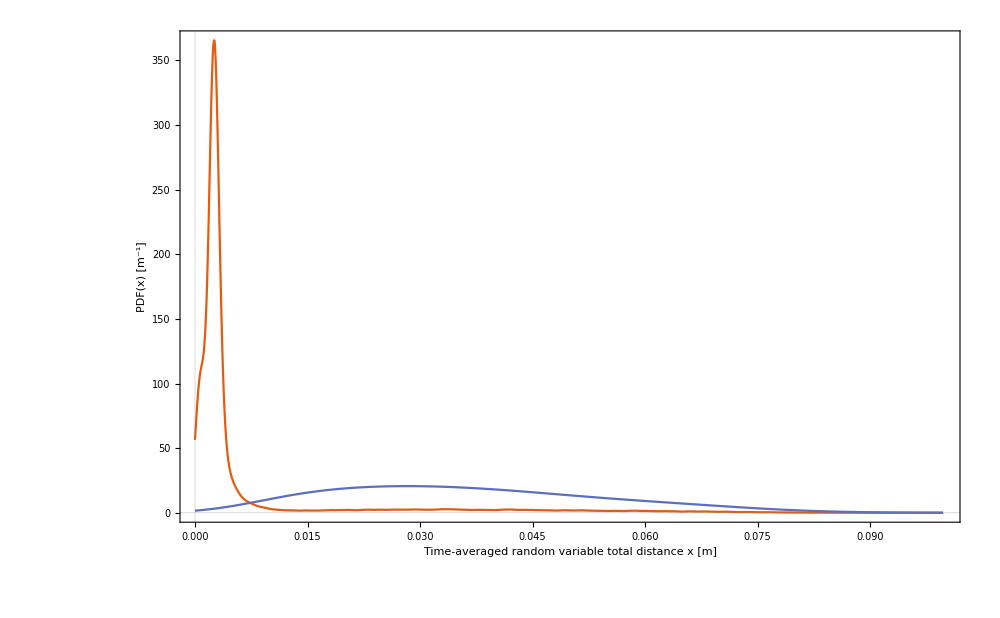

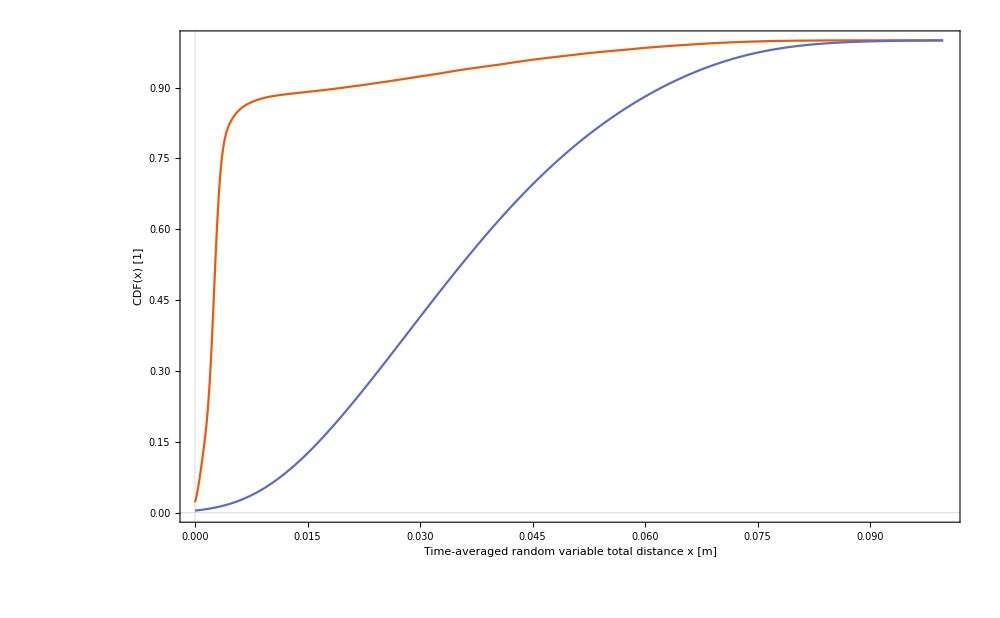

```mathematica
(* OLD *)
t1=10^5;
t2=10^6;

label[3][-1]=DisplayForm@Row[{
SubscriptBox[Style["D",FontFamily->"CMU Serif",Italic,30],Style["discrete",FontFamily->"CMU Serif",Plain,16]],
Row[{
Style["(",FontFamily->"CMU Serif",Italic,30],
Style[ToString[t1*10./(4*10^6)],FontFamily->"CMU Serif",Plain,30],
Style[" s",FontFamily->"CMU Serif",Plain,30],
Style[", ",FontFamily->"CMU Serif",Plain,30],
Style[ToString[t2*10./(4*10^6)],FontFamily->"CMU Serif",Plain,30],
Style[" s",FontFamily->"CMU Serif",Plain,30],
Style[")",FontFamily->"CMU Serif",Italic,30]}],
Style[" [m]",FontFamily->"CMU Serif",Plain,30]}];

R[1]=Map[Internal`StringToDouble[#]&,Map[StringSplit[#," "][[2;;4]]&,Import[filepathindump<>"dump"<>ToString[t1],"List"][[10;;]]],{2}];
R[2]=Map[Internal`StringToDouble[#]&,Map[StringSplit[#," "][[2;;4]]&,Import[filepathindump<>"dump"<>ToString[t2],"List"][[10;;]]],{2}];
length=Length@R[1];
Rred[1]=R[1][[Sort@Table[RandomInteger[{1,length}],{i,600}]]];
Rred[2]=R[2][[Sort@Table[RandomInteger[{1,length}],{i,600}]]];
ListPlot@Sort@Flatten[Outer[Norm[#1-#2]&,Rred[1],Rred[2],1],1];
R[3]=Map[Internal`StringToDouble[#]&,Map[StringSplit[#," "][[3]]&,Import[filepathinhungarian<>"cost_"<>ToString[t1]<>"_"<>ToString[t2]<>".txt","List"][[6;;]]]];
ListPlot@Sort@R[3];
𝒟1=SmoothKernelDistribution[R[3],0.0005];
δx=0.0004;
kern=Table[HeavisideLambda[x],{x,-1,1,0.2}]/Total[Table[HeavisideLambda[x],{x,-1,1,0.2}]];
datacdf1={Table[x,{x,0,0.1-0.00025,0.000025}],ListConvolve[kern,Table[CDF[𝒟1,x],{x,0,0.1,0.000025}]]}ᵀ;datapdf1={Table[x,{x,0,0.1-0.00025,0.000025}],ListConvolve[kern,Table[PDF[𝒟1,x],{x,0,0.1,0.000025}]]}ᵀ;
ListPlot[datacdf1,PlotRange->{All,{0,1}}];
ListPlot[datapdf1,PlotRange->{{0,0.01},All}];
R12=Flatten[Outer[Norm[#1-#2]&,Rred[1],Rred[2],1],1];
𝒟2=SmoothKernelDistribution[R12,0.005];
datacdf2={Table[x,{x,0,0.1-0.00025,0.000025}],ListConvolve[kern,Table[CDF[𝒟2,x],{x,0,0.1,0.000025}]]}ᵀ;datapdf2={Table[x,{x,0,0.1-0.00025,0.000025}],ListConvolve[kern,Table[PDF[𝒟2,x],{x,0,0.1,0.000025}]]}ᵀ;
ListPlot[datacdf2,PlotRange->{All,{0,1}}];
ListPlot[datapdf2];
g3[1]=ListLinePlot[{datapdf1,datapdf2},PlotRange->{{0,0.1},{0,All}},PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],FrameLabel->{label[3][0],label[3][1][1]},FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->{1000,700},ColorFunctionScaling->False]
g3[2]=ListLinePlot[{datacdf1,datacdf2},PlotRange->{{0,0.1},{0,All}},PlotRangePadding->0,
PlotTheme->"Scientific",
LabelStyle->Directive[Black,FontColor->Black,32,FontFamily->"CMU Serif",Italic],
FrameStyle->Directive[Black,FontColor->Black,FontFamily->"CMU Serif",Plain],FrameLabel->{label[3][0],label[3][1][2]},FrameTicks->{{Automatic,None},{Automatic,None}},
ImageSize->{1000,700},ColorFunctionScaling->False]
(* Map[{#[[1]],#[[2]]-datapdf1[[-1,2]]}&,datapdf1] *)
(* Map[{#[[1]],#[[2]]/datacdf1[[-1,2]]}&,datacdf1] *)
```

```mathematica
Export[filepathoutdistancedistribution<>"distances_pdf_100k_1000k.png",g3[1],"PNG",ImageResolution->300];
Export[filepathoutdistancedistribution<>"distances_cdf_100k_1000k.png",g3[2],"PNG",ImageResolution->300];
```